# NEAT

студент 3 курса 5 группы
Лицкевич Данила
20-12-2020

# NEAT

## 0. Info

https://towardsdatascience.com/neat-an-awesome-approach-to-neuroevolution-3eca5cc7930f

## 1. Individuals

## Generating Population

### Nodes

#### kmActivationFunc

```mathematica
kmActivationFunc[id_]:=
Switch[id,
0, #&,
1,Tanh[#]&,
2,LogisticSigmoid[#]&,
3,Sin[#]&,
4,UnitStep[#]&,
5,Ramp[#]&
]
```

#### kmNode

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
ClearAll[kmNode]
kmNode[id_,layer_,totalFuncs_:5]:=<|
"nodeId"->id,
"layer"->layer,
"inputSum"->0,
"bias"->RandomReal[{-1,1}],
"activationFunc"->RandomInteger[totalFuncs],
"output"->0
|>
```

```mathematica
kmNodeOutput[node_,prevNodes_]:=
Join[node,<|"inputSum"->#,"output"->node["bias"]+kmActivationFunc[node["activationFunc"]][#]|>]&[Total[prevNodes⟦All,"output"⟧]]
```

```mathematica
kmNode[1,1]
kmNodeOutput[%,{kmNode[2,1]~Join~<|"output"->12|>,kmNode[3,2]~Join~<|"output"->2|>}]
```

<|nodeId→1,layer→1,inputSum→0,bias→-0.937718,activationFunc→1,output→0|>

<|nodeId→1,layer→1,inputSum→14,bias→-0.937718,activationFunc→1,output→0.0622819|>

### Connections

```mathematica
CantorPairing[x_,y_]:=((x+y)(x+y+1))/2+y
```

#### kmConnection

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
kmConnection[{in_,out_},weight_:1]:=<|
"input"->in,
"output"->out,
"weight"->RandomReal[{-weight,weight}],
"enabled"->True,
"inovation"->CantorPairing[in,out]
|>
```

### Individual

Input and output nodes are not evolved in the node gene list. Hidden nodes can be added or removed.

```mathematica
ClearAll[kmAddIndividual]
SetAttributes[kmAddIndividual,HoldFirst]
kmAddIndividual[population_,hidden_:0]:=
AppendTo[population["individuals"],
<|
"input"->population["input"],
"output"->population["output"],
"total"->population["input"]+population["output"],
"fitness"->∞,
"nodes"->Join[
kmNode[#,1,0]&/@Range[population["input"]],
kmNode[#,2]&/@(population["input"]+Range[population["output"]])
],
"connections"->(kmConnection[#]&/@
Flatten[
Outer[
{#1,#2}&,
Range[population["input"]],
Range[population["input"]+1,population["input"]+population["output"]]
],1])
|>]
```

### Population

Input — количество входов;
Output — количество выходов;

```mathematica
kmPopulation[in_,out_,options___]:=<|
"input"->in,
"output"->out,
"best"-><|"fitness"->+∞|>,
"history"->{},
"size"->0,
(*"inovations"->{},*)
"individuals"->{},
"params"-><|
"addConnRate"->0.8,
"removeConnRate"->0.1,
"addNodeRate"->0.7,
"removeNodeRate"->0.05
|>
|>~Join~options
```

### Connection' s logics

#### kmFindNode

```mathematica
kmFindNode[individual_,id_]:=
First@FirstPosition[individual["nodes"],<|"nodeId"->id,___|>]
```

```mathematica
kmFindNode[testPop["individuals"]⟦1⟧,3]
```

NotFound

```mathematica
testPop[["individuals",1,"nodes",kmFindNode[testPop["individuals"]⟦1⟧,2]]]=1
```

Set::noval: Symbol testPop in part assignment does not have an immediate value.

1

#### kmInNodes

Finds all nodes which are  IN nodes for the node

```mathematica
kmInNodes[nodeId_,connections_]:=
Reap[
If[nodeId==#["output"],Sow[#["input"]]]&/@connections;
]//Last//Last
```

```mathematica
kmInNodes[2,{kmConnection[{1,2}],kmConnection[{3,2}]}]
```

{1,3}

#### kmExistConnectionQ

```mathematica
kmExistConnectionQ[connection:{in_,out_},connections_]:= 
Or@@({#["input"],#["output"]}==connection&/@connections)
```

### kmAddConnection

```mathematica
SetAttributes[kmAddConnection,HoldFirst]
kmAddConnection[population_,individualId_,conn:{in_,out_}]:= 
Block[{
individual=population["individuals"]⟦individualId⟧
},
individual⟦"connections"⟧=Join[
individual["connections"],
If[individual["nodes"]⟦in,"layer"⟧<individual["nodes"]⟦out,"layer"⟧,{kmConnection[conn]},{}]
];
population⟦"individuals", individualId⟧=individual
]
```

### kmAddNode

```mathematica
SetAttributes[kmAddNode,HoldFirst]
kmAddNode[population_,individualId_,connectionId_]:= 
Block[{
individual=population["individuals"]⟦individualId⟧,
connection, oldOutNodePos
},
connection=individual["connections"]⟦connectionId⟧;
individual⟦"connections",connectionId,"enabled"⟧=False;

oldOutNodePos=kmFindNode[individual,connection["output"]];
individual⟦"total"⟧+=1;
individual⟦"nodes"⟧=
Append[individual["nodes"],kmNode[individual["total"],individual⟦"nodes",oldOutNodePos,"layer"⟧]];
individual⟦"nodes",oldOutNodePos,"layer"⟧+=1;

individual⟦"connections"⟧=Join[
{kmConnection[{connection["input"],#}],
kmConnection[{#,connection["output"]}]}&[individual["total"]],
individual["connections"]
];
population⟦"individuals", individualId⟧=individual
]
```

### Tests

```mathematica
testPop=kmPopulation[2,3]
kmAddIndividual[testPop]
kmAddIndividual[testPop]
kmAddNode[testPop,1,1]
```

<|input→2,output→3,best→<|fitness→∞|>,history→{},size→0,individuals→{},params→<|addConnRate→0.8,removeConnRate→0.1,addNodeRate→0.7,removeNodeRate→0.05|>|>

{<|input→2,output→3,total→5,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.094656,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.348278,activationFunc→0,output→0|>,<|nodeId→3,layer→2,inputSum→0,bias→-0.334976,activationFunc→4,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.562258,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→0.144634,activationFunc→0,output→0|>},connections→{<|input→1,output→3,weight→0.493161,enabled→True,inovation→13|>,<|input→1,output→4,weight→-0.614912,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.570537,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.260269,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.210817,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.544719,enabled→True,inovation→33|>}|>}

{<|input→2,output→3,total→5,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.094656,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.348278,activationFunc→0,output→0|>,<|nodeId→3,layer→2,inputSum→0,bias→-0.334976,activationFunc→4,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.562258,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→0.144634,activationFunc→0,output→0|>},connections→{<|input→1,output→3,weight→0.493161,enabled→True,inovation→13|>,<|input→1,output→4,weight→-0.614912,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.570537,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.260269,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.210817,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.544719,enabled→True,inovation→33|>}|>,<|input→2,output→3,total→5,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→0.743434,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.571034,activationFunc→0,output→0|>,<|nodeId→3,layer→2,inputSum→0,bias→0.267832,activationFunc→2,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.291945,activationFunc→5,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.435731,activationFunc→2,output→0|>},connections→{<|input→1,output→3,weight→0.854312,enabled→True,inovation→13|>,<|input→1,output→4,weight→0.87814,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.762762,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.651242,enabled→True,inovation→18|>,<|input→2,output→4,weight→-0.3993,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.89225,enabled→True,inovation→33|>}|>}

<|input→2,output→3,total→6,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.094656,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.348278,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→-0.334976,activationFunc→4,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.562258,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→0.144634,activationFunc→0,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→-0.715906,activationFunc→2,output→0|>},connections→{<|input→1,output→6,weight→0.938117,enabled→True,inovation→34|>,<|input→6,output→3,weight→-0.645611,enabled→True,inovation→48|>,<|input→1,output→3,weight→0.493161,enabled→False,inovation→13|>,<|input→1,output→4,weight→-0.614912,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.570537,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.260269,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.210817,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.544719,enabled→True,inovation→33|>}|>

```mathematica
Dynamic@testPop
```

## Individual decoding

#### kmNodesToLayers

```mathematica
ClearAll[kmNodesToLayers]
kmNodesToLayers[individual_]:=
Module[
{maxLayer=Max[individual[["nodes",All,"layer"]]],
nodes
},
Join[individual,
<|
"maxLayer"->maxLayer,
"nodesLayered"->Function[{layer},Select[individual["nodes"],#["layer"]==layer&]]/@Range[maxLayer]
|>
]
]
```

```mathematica
kmNodesToLayers[testPop[["individuals",1]]]
```

<|input→2,output→3,total→6,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.773344,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.39588,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→0.931847,activationFunc→4,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.356916,activationFunc→1,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.0500305,activationFunc→2,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.932912,activationFunc→0,output→0|>},connections→{<|input→1,output→6,weight→-0.207087,enabled→True,inovation→34|>,<|input→6,output→3,weight→0.628047,enabled→True,inovation→48|>,<|input→1,output→3,weight→-0.209763,enabled→False,inovation→13|>,<|input→1,output→4,weight→0.578772,enabled→True,inovation→19|>,<|input→1,output→5,weight→0.525658,enabled→True,inovation→26|>,<|input→2,output→3,weight→0.89998,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.897321,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.440981,enabled→True,inovation→33|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.773344,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.39588,activationFunc→0,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.356916,activationFunc→1,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.0500305,activationFunc→2,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.932912,activationFunc→0,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→0.931847,activationFunc→4,output→0|>}}|>

#### kmIndividualsToLayers

```mathematica
ClearAll[kmIndividualsPrepare]
SetAttributes[kmIndividualsPrepare,HoldFirst]
kmIndividualsPrepare[population_]:=
population⟦"individuals"⟧=kmNodesToLayers[#]&/@population["individuals"]
```

```mathematica
kmIndividualsPrepare[testPop]
```

{<|input→2,output→3,total→6,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.773344,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.39588,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→0.931847,activationFunc→4,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.356916,activationFunc→1,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.0500305,activationFunc→2,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.932912,activationFunc→0,output→0|>},connections→{<|input→1,output→6,weight→-0.207087,enabled→True,inovation→34|>,<|input→6,output→3,weight→0.628047,enabled→True,inovation→48|>,<|input→1,output→3,weight→-0.209763,enabled→False,inovation→13|>,<|input→1,output→4,weight→0.578772,enabled→True,inovation→19|>,<|input→1,output→5,weight→0.525658,enabled→True,inovation→26|>,<|input→2,output→3,weight→0.89998,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.897321,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.440981,enabled→True,inovation→33|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.773344,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.39588,activationFunc→0,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.356916,activationFunc→1,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.0500305,activationFunc→2,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.932912,activationFunc→0,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→0.931847,activationFunc→4,output→0|>}}|>,<|input→2,output→3,total→5,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.217769,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.268548,activationFunc→0,output→0|>,<|nodeId→3,layer→2,inputSum→0,bias→-0.175238,activationFunc→5,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.32843,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→0.972977,activationFunc→1,output→0|>},connections→{<|input→1,output→3,weight→-0.410658,enabled→True,inovation→13|>,<|input→1,output→4,weight→0.2864,enabled→True,inovation→19|>,<|input→1,output→5,weight→0.0146007,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.655525,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.150777,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.166752,enabled→True,inovation→33|>},maxLayer→2,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.217769,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.268548,activationFunc→0,output→0|>},{<|nodeId→3,layer→2,inputSum→0,bias→-0.175238,activationFunc→5,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.32843,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→0.972977,activationFunc→1,output→0|>}}|>}

#### kmInitFirstLayer

```mathematica
ClearAll[kmInitFirstLayer]
kmInitFirstLayer[nodes_,inputs_List]:=
MapThread[Join[#1,<|"output"->#2|>]&,{SortBy[nodes,#["nodeId"]&],inputs}]
```

#### kmGetNodesLayered

```mathematica
ClearAll[kmGetNodesLayered]
kmGetNodesLayered[individual_,nodeIds_]:=
Flatten[Function[{nodeId},Select[individual["nodesLayered"]//Flatten,#["nodeId"]==nodeId&,1]]/@nodeIds]
```

#### kmInNodesLayered

```mathematica
ClearAll[kmInNodesLayered]
kmInNodesLayered[individual_,node_]:=kmGetNodesLayered[individual,kmInNodes[node["nodeId"],individual["connections"]]]
```

```mathematica
kmInNodesLayered[testPop["individuals"][[1]],<|"nodeId"->3,"layer"->1,"inputSum"->0,"bias"->-0.012840107337042994,"activationFunc"->0,"output"->1|>]
```

{<|nodeId→6,layer→2,inputSum→0,bias→0.932912,activationFunc→0,output→0|>,<|nodeId→1,layer→1,inputSum→0,bias→-0.773344,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.39588,activationFunc→0,output→0|>}

#### kmIndividualToFunction

```mathematica
ClearAll[kmIndividualEvaluate]
kmIndividualEvaluate[individual_,inputs_List]:=
Module[
{individualCopy=individual},
individualCopy[["nodesLayered",1]]=kmInitFirstLayer[individualCopy["nodesLayered"]//First,inputs];
Function[{layer},
individualCopy[["nodesLayered",layer]]=
Function[{node},
kmNodeOutput[node,kmInNodesLayered[individualCopy,node]]
]/@individualCopy[["nodesLayered",layer]]
]/@Range[2,individual["maxLayer"]];
kmGetNodesLayered[individualCopy,Range[#+1,#+individual["output"]]&[individual["input"]]]⟦All,"output"⟧
]
```

```mathematica
kmIndividualEvaluate[testPop["individuals"][[1]],{.1,.2}]
```

{1.93185,0.648229,0.524412}

## Population viewing (realisatoin Delayed)

```mathematica
testIndividual=<|"input"->2,"output"->3,"hidden"->4,"connections"->{<|"input"->1,"output"->5,"weight"->-0.9628618224751473,"enabled"->1,"inovation"->1|>,<|"input"->3,"output"->4,"weight"->0.22393191857363837,"enabled"->1,"inovation"->2|>,<|"input"->4,"output"->6,"weight"->-0.4785485230617863,"enabled"->1,"inovation"->3|>,<|"input"->6,"output"->5,"weight"->0.45075859641862426,"enabled"->1,"inovation"->4|>,<|"input"->8,"output"->5,"weight"->0.5039873848534051,"enabled"->1,"inovation"->5|>}|>;
```

### Individual viewing

#### kmNodes

1  – in node
2  – out node
3  – hidden node

```mathematica
kmNodes[type_,nodesQuant_,layer_]:=
{Switch[type,1,Red,2,Blue,3,Gray,True,Black],Disk[{-nodesQuant+2#,layer},0.25]&/@Range[nodesQuant]}
```

#### kmViewIndividual

```mathematica
kmViewIndividual[individ_]:=
Graphics[{kmNodes[1,3,1],kmNodes[2,2,2]}]
```

```mathematica
Dynamic@kmViewIndividual[1]
```

```mathematica
Graph
```

### Population viewing

## Population mutations

### kmAllMutateNodes

```mathematica
SetAttributes[kmAllMutateNodes,HoldFirst]
kmAllMutateNodes[population_]:= 
If[
RandomReal[]<population["params","addNodeRate"],
kmAddNode[population,#,RandomInteger[{1,Length[testPop⟦"individuals",#,"connections"⟧]}]]
]&/@Range[Length[population["individuals"]]]
```

### kmAllMutateConnections

```mathematica
SetAttributes[kmAllMutateConnections,HoldFirst]
kmAllMutateConnections[population_]:= 
If[
RandomReal[]<population["params","addConnRate"],
kmAddConnection[population,#,RandomSample[population[["individuals",#,"nodes"]],2]⟦All,"nodeId"⟧]
]&/@Range[Length[population["individuals"]]]
```

### kmCrossover

#### kmNodesFromConns

```mathematica
kmNodesFromConnections[connections_]:= 
Union[Part[connections,All,"input"],Part[connections,All,"output"]]
```

#### kmCrossover

```mathematica
kmCrossover[parent1_,parent2_]:= 
Module[
{conns1,conns2, nodes1,nodes2, 
separator= RandomChoice[
Join[parent1["connections"],parent2["connections"]]
]["inovation"]
},
conns1 =Select[parent1["connections"],#["inovation"]≤separator&] ;
conns2=Select[parent2["connections"],#["inovation"]>separator&];
nodes1=kmNodesFromConnections[conns1];
nodes2=Complement[kmNodesFromConnections[conns2],nodes1];
<|
"input"->parent1["input"],
"output"->parent1["output"],
"total"->Length[Join[nodes1,nodes2]],
"nodes"->Join[parent1["nodes"]⟦nodes1⟧,parent2["nodes"]⟦nodes2⟧],
"connections"->Join[conns1,conns2]
|>
]
```

```mathematica
kmCrossover[testPop[["individuals",1]],testPop[["individuals",2]]]
```

<|input→2,output→3,total→5,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→0.509775,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.766798,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→-0.367035,activationFunc→5,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→-0.898505,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→0.365519,activationFunc→3,output→0|>},connections→{<|input→1,output→3,weight→0.551129,enabled→False,inovation→13|>,<|input→1,output→4,weight→0.540787,enabled→True,inovation→19|>,<|input→1,output→5,weight→0.0877997,enabled→True,inovation→26|>,<|input→2,output→3,weight→0.724592,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.413499,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.753756,enabled→True,inovation→33|>}|>

## Population evolution

### Fitness

```mathematica
ClearAll[kmAssessFitness]
SetAttributes[kmAssessFitness,HoldFirst]
kmAssessFitness[population_Symbol,fitness_]:=Module[
{min},
kmIndividualsPrepare[population];
min=Min[population["fitness"]=fitness/@population["individuals"]];
AppendTo[population["history"],
If[min<population["best","fitness"],{
population["best","individual"]=population⟦"individuals",Position[population["fitness"],min]⟦1,1⟧⟧,
population["best","fitness"]=min
},
{population⟦"individuals",Position[population["fitness"],min]⟦1,1⟧⟧,min}
]
]
]
```

### Elimination

```mathematica
SetAttributes[kmElimination,HoldFirst]
kmElimination[population_,replaceIndividual_]:=
Block[{
index=RandomChoice[1/(Exp/@population["fitness"])->Range[population["size"]]]
},
population⟦"individuals",index⟧=replaceIndividual;
]
```

### Selection

```mathematica
SetAttributes[kmSelection,HoldFirst]
kmSelection[population_]:=
RandomChoice[(#/Total[#]&)@(Exp/@population["fitness"])->Range[population["size"]]]
```

### Evolution

```mathematica
SetAttributes[kmEvolveOne,HoldFirst]
kmEvolveOne[population_,fitness_]:=
Catch[
Block[{individualId,save},
kmAssessFitness[population,fitness];
individualId=kmSelection[population];

If[RandomReal[]<population⟦"params","crossOverRate"⟧,

population⟦"state"⟧=population⟦"state"⟧+{1,0,0};
kmElimination[population,#]&[
kmCrossover[population⟦"individuals",individualId⟧,
population⟦"individuals",RandomInteger[{1,population["size"]}]⟧
]];
,
If[
RandomReal[]<population⟦"params","addConnRate"⟧,
population⟦"state"⟧=population⟦"state"⟧+{1,0,0};
kmAddConnection[population,individualId,RandomSample[population[["individuals",individualId,"nodes"]],2]⟦All,"nodeId"⟧];
];
If[
RandomReal[]<population⟦"params","addNodeRate"⟧,
population⟦"state"⟧=population⟦"state"⟧+{0,0,1};
kmAddNode[population,individualId,RandomInteger[{1,Length[testPop⟦"individuals",individualId,"connections"⟧]}]];
]
];

]
];
```

## Test Task 1 - simple binary Classification in 2D

### kmClassificationTask – generate a task

```mathematica
ClearAll[kmClassificationTask]
kmClassificationTask[function_,testersNumber_:50,rangeX_:{0,2},rangeY_:{-1,1}]:=
Block[{targets,
testers
},
testers =Thread[ {RandomReal[rangeX,testersNumber],RandomReal[rangeY,testersNumber]}];
targets=If[function[#1]>#2,1,0]&@@@testers;
<|"function"->function,"testers"->testers,"targets"->targets,"rangeX"->rangeX, "rangeY"->rangeY|>
]
```

```mathematica
kmClassificationTask[Sin]
```

<|function→Sin,testers→{{-0.0104605,0.93808},{0.60224,0.003257},{0.319561,-0.29237},{-0.658019,0.382238},{0.5557,0.397428},{-0.312059,-0.402993},{-0.742417,0.98064},{-0.889611,0.905282},{0.39976,0.947142},{-0.398031,-0.967997},{0.601821,-0.794314},{0.42545,-0.480677},{0.792797,0.806598},{0.68164,0.652832},{0.807282,0.943339},{-0.782971,0.915443},{0.934121,-0.0547549},{0.576396,0.453487},{-0.69901,-0.507395},{0.829977,-0.560057},{-0.500424,0.0303878},{-0.0141205,-0.646484},{0.697163,0.761199},{-0.0515078,-0.285925},{0.0320183,0.412191},{-0.777888,-0.803011},{-0.987973,-0.140237},{-0.902711,-0.766552},{-0.975502,0.63867},{-0.0437557,0.845757},{0.502928,-0.185673},{0.743217,-0.454488},{0.383341,-0.744764},{-0.496993,-0.532447},{-0.178948,-0.684196},{0.60393,0.751718},{-0.327763,-0.0929231},{-0.654897,0.298653},{0.878849,-0.290828},{-0.417305,0.0306268},{0.324645,-0.733842},{-0.705499,0.172848},{0.996477,0.962945},{-0.479792,-0.970902},{0.447937,0.52975},{-0.815149,-0.15747},{-0.305691,-0.233782},{-0.790617,0.572875},{0.553275,-0.550667},{-0.0888072,0.910306}},targets→{0,1,1,0,1,1,0,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,1,0,1,0,0,0,0,1,1,1,1,1,0,0,0,1,0,1,0,0,1,0,0,0,0,1,0},rangeX→{-1,1},rangeY→{-1,1}|>

### Additional functions

#### kmPredictionToAnswer

```mathematica
ClearAll[kmPredictionToAnswer]
SetAttributes[kmPredictionToAnswer,Listable]
kmPredictionToAnswer[prediction_]:=If[LogisticSigmoid[prediction]>0.5,1,0]
```

#### kmClassificationAccuracy

```mathematica
kmClassificationAccuracy[targets_,predictions_]:=N@EuclideanDistance[targets,predictions]
```

### kmShowPredictions

#### NonZeroQ

```mathematica
ClearAll[NonZeroQ]
NonZeroQ[n_]:=(n=!=0)&&NumberQ[n]
```

#### kmShowTestersEpilog

```mathematica
ClearAll[kmShowTestersEpilog]
kmShowTestersEpilog[testers_,targets_,predictions_]:=
{AbsolutePointSize[10],{
Red,Point@Extract[testers,Position[#,_?NonZeroQ]],
Blue,Point@Extract[testers,Position[#,0]]}
}&[targets-kmPredictionToAnswer[predictions]]
```

#### kmShowPredictions

```mathematica
ClearAll[kmShowPredictions]
kmShowPredictions[task_,predictions_]:=
With[{
function =task["function"]
},
Labeled[
Plot[function[x],{x,Sequence@@task["rangeX"]},
Epilog->kmShowTestersEpilog[task["testers"],task["targets"],predictions],
PlotRange->{task["rangeX"],task["rangeY"]},AspectRatio->1,Axes->True
],
"Error: "<>ToString@kmClassificationAccuracy[task["targets"],predictions]
]

]
```

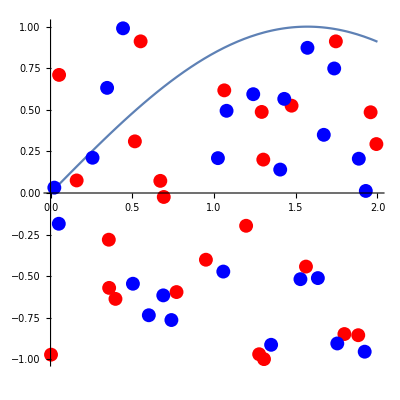
-Graphics-Error: 7.96782

```mathematica
kmShowPredictions[kmClassificationTask[Sin],RandomReal[{-1,1},50]]
```